```mathematica
SetDirectory["/Users/naomi/Projects"]
```

/Users/naomi/Projects

```mathematica
Get["QSIM/QSIM_basicFunctions.m"]
Get["QSIM/QSIM_measurement.m"]
Get["QSIM/QSIM_stabilizers.m"]
Get["QSIM/QSIM_nonlocal.m"]
Get["QSIM/QSIM_noise.m"]
Get["QSIM/QSIM_superoperators.m"]
Get["QSIM/QSIM_errorAnalysis.m"]
```

```mathematica
rot[θ_]:=Cos[θ/2]*id-I*Sin[θ/2]*pY
```

```mathematica
proj[θ_]:=CT[rot[θ]].projEvenMatrix[1].rot[θ]
```

### Normal Distribution

#### simulation data

```mathematica
findConstants[Ω_,nSamples_]:=Module[{state,s,ss,p,measureState,eval,evec,z1,peven,podd,ypeven,ypodd,fidelities},


ss=RandomVariate[NormalDistribution[0,Ω],nSamples];
measureState =phi0;
z1=KP[pZ,id];

For[i=1,i<nSamples,i++,
s = ss⟦i⟧;
state = phi0;
p=KP[ proj[s],id];
state = p.state.CT[p];

If[Random[]<0.5, state = z1.state.CT[z1]];

measureState=measureState+state;


];

measureState = measureState/Tr[measureState];

(*{eval,evec}=createSuperoperator[measureState];*)

(* Find ideal superoperators and test against the one found *)

peven = KP[projEvenMatrix[1],id].phi0. KP[projEvenMatrix[1],id];
podd =KP[projOddMatrix[1],id].phi0. KP[projOddMatrix[1],id];
ypeven =KP[pY.projEvenMatrix[1],id].phi0.CT[KP[pY.projEvenMatrix[1],id]];
ypodd =KP[pY.projOddMatrix[1],id].phi0.CT[KP[pY.projOddMatrix[1],id]];

fidelities=2*Fidelity[#,measureState]&/@{peven,podd,ypeven,ypodd};
fidelities = Join[fidelities[[1;;3]],{(1-Plus@@fidelities)}]

]
```

#### Analytic solution

```mathematica
sol1Normal=Integrate[PDF[NormalDistribution[0,Ω],θ]*Cos[θ/2]^4,{θ,-Pi,Pi}]
```

1/16 (6 Erf[π/(√2 Ω)]+ⅇ^(-2 Ω^2) (4 ⅇ^((3 Ω^2)/2) (Erf[(π-ⅈ Ω^2)/(√2 Ω)]+Erf[(π+ⅈ Ω^2)/(√2 Ω)])+Erf[(π-2 ⅈ Ω^2)/(√2 Ω)]+Erf[(π+2 ⅈ Ω^2)/(√2 Ω)]))

```mathematica
sol2Normal=Integrate[PDF[NormalDistribution[0,Ω],θ]*Sin[θ/2]^4,{θ,-Pi,Pi}]
```

1/16 (6 Erf[π/(√2 Ω)]+ⅇ^(-2 Ω^2) (-4 ⅇ^((3 Ω^2)/2) (Erf[(π-ⅈ Ω^2)/(√2 Ω)]+Erf[(π+ⅈ Ω^2)/(√2 Ω)])+Erf[(π-2 ⅈ Ω^2)/(√2 Ω)]+Erf[(π+2 ⅈ Ω^2)/(√2 Ω)]))

```mathematica
sol3Normal=Integrate[PDF[NormalDistribution[0,Ω],θ]*Sin[θ/2]^2*Cos[θ/2]^2,{θ,-Pi,Pi}]
```

1/16 (2 Erf[π/(√2 Ω)]+ⅇ^(-2 Ω^2) (-2+Erfc[(π-2 ⅈ Ω^2)/(√2 Ω)]+Erfc[(π+2 ⅈ Ω^2)/(√2 Ω)]))

#### Plots

```mathematica
dataNormal =Thread@(Thread[#]&/@({ConstantArray[#,4],findConstants[#,10000]}&/@(Range[50]/10.)));
```

```mathematica
t1Normal = Plot[{sol1Normal,sol2Normal,sol3Normal},{Ω,0,5}];
```

```mathematica
t2Normal=Plot[{sol1Normal,sol2Normal,sol3Normal},{Ω,Pi/2,Pi}];
t3Normal=Plot[{sol1Normal,sol2Normal,sol3Normal},{Ω,Pi,5}];
```

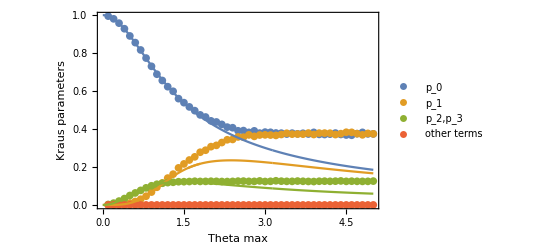

```mathematica
Show[ListPlot[dataNormal,PlotLegends->{"p_0","p_1","p_2,p_3","other terms"},Frame->True,FrameLabel->{"Theta max","Kraus parameters"}],t1Normal,t2Normal,t3Normal]
```

### Uniform Distribution

#### simulation data

```mathematica
findConstants[Ω_,nSamples_]:=Module[{state,s,ss,p,measureState,eval,evec,z1,peven,podd,ypeven,ypodd,fidelities},

ss=RandomVariate[UniformDistribution[{-Ω,Ω}],nSamples];
measureState =phi0;
z1=KP[pZ,id];

For[i=1,i<nSamples,i++,
s = ss⟦i⟧;
state = phi0;
p=KP[ proj[s],id];
state = p.state.CT[p];

If[Random[]<0.5, state = z1.state.CT[z1]];

measureState=measureState+state;


];

measureState = measureState/Tr[measureState];

(*{eval,evec}=createSuperoperator[measureState];*)

(* Find ideal superoperators and test against the one found *)

peven = KP[projEvenMatrix[1],id].phi0. KP[projEvenMatrix[1],id];
podd =KP[projOddMatrix[1],id].phi0. KP[projOddMatrix[1],id];
ypeven =KP[pY.projEvenMatrix[1],id].phi0.CT[KP[pY.projEvenMatrix[1],id]];
ypodd =KP[pY.projOddMatrix[1],id].phi0.CT[KP[pY.projOddMatrix[1],id]];

fidelities=2*Fidelity[#,measureState]&/@{peven,podd,ypeven,ypodd};
fidelities = Join[fidelities[[1;;3]],{(1-Plus@@fidelities)}]

]
```

#### Analytic solution

```mathematica
sol1=Integrate[PDF[UniformDistribution[{-Ω,Ω}],θ]*Cos[θ/2]^4,{θ,-Pi,Pi}]
```

Piecewise[{{(3 π)/(8 Ω), Ω>π}, {(3 Ω+4 Sin[Ω]+Cos[Ω] Sin[Ω])/(8 Ω), 0<Ω≤π}, {0, True}}]

```mathematica
sol2=Integrate[PDF[UniformDistribution[{-Ω,Ω}],θ]*Sin[θ/2]^4,{θ,-Pi,Pi}]
```

Piecewise[{{(3 π)/(8 Ω), Ω>π}, {(3 Ω-4 Sin[Ω]+Cos[Ω] Sin[Ω])/(8 Ω), 0<Ω≤π}, {0, True}}]

```mathematica
sol3=Integrate[PDF[UniformDistribution[{-Ω,Ω}],θ]*Sin[θ/2]^2*Cos[θ/2]^2,{θ,-Pi,Pi}]
```

Piecewise[{{π/(8 Ω), Ω>π}, {(Ω-Cos[Ω] Sin[Ω])/(8 Ω), 0<Ω≤π}, {0, True}}]

#### Plots

```mathematica
dataUniform =Thread@(Thread[#]&/@({ConstantArray[#,4],findConstants[#,10000]}&/@(Range[31]/10.)));
```

```mathematica
t1Uniform = Plot[{sol1,sol2,sol3},{Ω,0,Pi}];
```

```mathematica
t2=Plot[{sol1,sol2,sol3},{Ω,Pi,2*Pi}];
t3=Plot[{sol1,sol2,sol3},{Ω,Pi,5}];
```

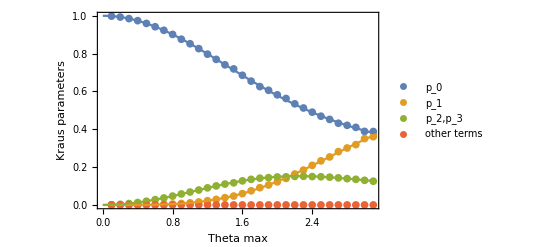

(ⅇ^(-θ^2/(2 Ω^2)))/(√(2 π) Ω)

```mathematica
Show[ListPlot[dataUniform,PlotLegends->{"p_0","p_1","p_2,p_3","other terms"},Frame->True,FrameLabel->{"Theta max","Kraus parameters"}],t1Uniform]
```